# 2021 - 09 - 01 · Ξ analysis

## https://arxiv.org/abs/2104.05122 Script to generate pictures used in PhD thesis of WB. Please avoid direct copying of these pictures without permission, as it will explicitly clash with already published work; name[at]uj.edu.pl name = w.bruzda

## MaTeX

```mathematica
ResourceFunction["MaTeXInstall"][]
```

```mathematica
Paclet["MaTeX","1.7.8",<>]
```

```mathematica
(* customized path (I use m$win only at the workplace...) *)
ConfigureMaTeX["Ghostscript"->"C:\\Program Files\\gs\\gs9.54.0\\bin\\gswin64c.exe"]
```

```mathematica
ConfigureMaTeX[]
```

```mathematica
<<MaTeX`
```

```mathematica
MaTeX["x^{12}\Xi(\sqrt{x^3})"]
```

-Graphics-

## def. of partial transpose and reshuffling for general dimension d

```mathematica
T2[a_]:=Module[{dim,sdim,ret}, (* partial transpose X^Subscript[T, 2] - courtesy of GRM *)
dim=Dimensions[a]⟦1⟧;
sdim=Sqrt[dim];
ret=Partition[a,{sdim,sdim}];
ret=Map[Transpose,ret,{2}];
ret=ArrayFlatten[ret];
Return[ret];
];

(* R2[M_]:=ArrayFlatten@Array[M⟦#2+d#1-d,#4+d#3-d⟧&,{d,d,d,d}] *)
RF[M_]:=Module[{d,ret},
d=Sqrt@Dimensions[M]⟦1⟧;
ret=ArrayFlatten@Array[M⟦#2+d#1-d,#4+d#3-d⟧&,{d,d,d,d}];
Return[ret]
];

Xi[M_]:=1/3(M+RF[T2[M]]+T2[RF[M]]);

SL[M_]:=Module[{d,ret}, (* in paper it is called E *)
d=Sqrt@Dimensions[M]⟦1⟧;
ret=d^2/(d^2-1)(1-Total[Eigenvalues[M.M†]^2]/Tr[M.M†]^2);
Return[ret];
]
```

## generic square matrix for d=2

```mathematica
X={{a11,a12,a13,a14},{a21,a22,a23,a24},{a31,a32,a33,a34},{a41,a42,a43,a44}};
MatrixForm/@{X,T2@X,RF@X}
Y=Xi@X;
Y//MatrixForm
Z=Y.Transpose[Y];
Z//MatrixForm//FullSimplify
```

{(a11 | a12 | a13 | a14
a21 | a22 | a23 | a24
a31 | a32 | a33 | a34
a41 | a42 | a43 | a44),(a11 | a21 | a13 | a23
a12 | a22 | a14 | a24
a31 | a41 | a33 | a43
a32 | a42 | a34 | a44),(a11 | a12 | a21 | a22
a13 | a14 | a23 | a24
a31 | a32 | a41 | a42
a33 | a34 | a43 | a44)}

(a11 | 1/3 (a12+a13+a21) | 1/3 (a12+a13+a21) | 1/3 (a14+a22+a23)
1/3 (a12+a13+a21) | 1/3 (a14+a22+a23) | 1/3 (a14+a22+a23) | a24
a31 | 1/3 (a32+a33+a41) | 1/3 (a32+a33+a41) | 1/3 (a34+a42+a43)
1/3 (a32+a33+a41) | 1/3 (a34+a42+a43) | 1/3 (a34+a42+a43) | a44)

(a11^2+1/9 (2 (a12+a13+a21)^2+(a14+a22+a23)^2) | 1/9 (3 a11 (a12+a13+a21)+(a14+a22+a23) (2 (a12+a13+a21)+3 a24)) | a11 a31+1/9 (2 (a12+a13+a21) (a32+a33+a41)+(a14+a22+a23) (a34+a42+a43)) | 1/9 (3 a11 (a32+a33+a41)+2 (a12+a13+a21) (a34+a42+a43)+3 (a14+a22+a23) a44)
1/9 (3 a11 (a12+a13+a21)+(a14+a22+a23) (2 (a12+a13+a21)+3 a24)) | 1/9 (a12+a13+a21)^2+2/9 (a14+a22+a23)^2+a24^2 | 1/9 (3 (a12+a13+a21) a31+2 (a14+a22+a23) (a32+a33+a41)+3 a24 (a34+a42+a43)) | 1/9 (a12+a13+a21) (a32+a33+a41)+2/9 (a14+a22+a23) (a34+a42+a43)+a24 a44
a11 a31+1/9 (2 (a12+a13+a21) (a32+a33+a41)+(a14+a22+a23) (a34+a42+a43)) | 1/9 (3 (a12+a13+a21) a31+2 (a14+a22+a23) (a32+a33+a41)+3 a24 (a34+a42+a43)) | a31^2+1/9 (2 (a32+a33+a41)^2+(a34+a42+a43)^2) | 1/9 (3 a31 (a32+a33+a41)+(a34+a42+a43) (2 (a32+a33+a41)+3 a44))
1/9 (3 a11 (a32+a33+a41)+2 (a12+a13+a21) (a34+a42+a43)+3 (a14+a22+a23) a44) | 1/9 (a12+a13+a21) (a32+a33+a41)+2/9 (a14+a22+a23) (a34+a42+a43)+a24 a44 | 1/9 (3 a31 (a32+a33+a41)+(a34+a42+a43) (2 (a32+a33+a41)+3 a44)) | 1/9 (a32+a33+a41)^2+2/9 (a34+a42+a43)^2+a44^2)

```mathematica
(* is Y orthogonal? (equiv. is Z identity?) *)
sss=NSolve[
{
Z⟦1,1⟧==1,
Z⟦1,2⟧==0,
Z⟦1,3⟧==0,
Z⟦1,4⟧==0,
Z⟦2,2⟧==1,
Z⟦2,3⟧==0,
Z⟦2,4⟧==0,
Z⟦3,3⟧==1,
Z⟦3,4⟧==0,
Z⟦4,4⟧==1
},
{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}]
```

{}

```mathematica
Y=ArrayReshape[{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}/.sss[[1]],{4,4}];
Y//MatrixForm//Chop
SL/@{Y,RF@Y,T2@Y}
Y.Transpose[Y]//MatrixForm//Expand//Chop
(* should fail, since there is no solution *)
```

ArrayReshape[{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}/.{}⟦1⟧,{4,4}]

{2 (1-Total[Eigenvalues[ArrayReshape[{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}/.{}⟦1⟧,{4,4}].ConjugateTranspose[ArrayReshape[{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}/.{}⟦1⟧,{4,4}]]]^2]/Tr[ArrayReshape[{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}/.{}⟦1⟧,{4,4}].ConjugateTranspose[ArrayReshape[{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}/.{}⟦1⟧,{4,4}]]]^2),ComplexInfinity,ComplexInfinity}

ArrayReshape[{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}/.{}⟦1⟧,{4,4}].Transpose[ArrayReshape[{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}/.{}⟦1⟧,{4,4}]]

## generic square matrix for d=3 (for d=4 Mathematica dies quickly, for d=6 Matlab/Octave calculations tentatively suggest the solution is empty...)

```mathematica
X={
{a11,a12,a13,a14,a15,a16,a17,a18,a19},
{b11,b12,b13,b14,b15,b16,b17,b18,b19},
{c11,c12,c13,c14,c15,c16,c17,c18,c19},
{d11,d12,d13,d14,d15,d16,d17,d18,d19},
{e11,e12,e13,e14,e15,e16,e17,e18,e19},
{f11,f12,f13,f14,f15,f16,f17,f18,f19},
{g11,g12,g13,g14,g15,g16,g17,g18,g19},
{h11,h12,h13,h14,h15,h16,h17,h18,h19},
{i11,i12,i13,i14,i15,i16,i17,i18,i19}
};
MatrixForm/@{X,T2@X,RF@X}
Y=Xi@X;
Y//MatrixForm
Z=Y.Transpose[Y];
Z//MatrixForm//Simplify
```

{(a11 | a12 | a13 | a14 | a15 | a16 | a17 | a18 | a19
b11 | b12 | b13 | b14 | b15 | b16 | b17 | b18 | b19
c11 | c12 | c13 | c14 | c15 | c16 | c17 | c18 | c19
d11 | d12 | d13 | d14 | d15 | d16 | d17 | d18 | d19
e11 | e12 | e13 | e14 | e15 | e16 | e17 | e18 | e19
f11 | f12 | f13 | f14 | f15 | f16 | f17 | f18 | f19
g11 | g12 | g13 | g14 | g15 | g16 | g17 | g18 | g19
h11 | h12 | h13 | h14 | h15 | h16 | h17 | h18 | h19
i11 | i12 | i13 | i14 | i15 | i16 | i17 | i18 | i19),(a11 | b11 | c11 | a14 | b14 | c14 | a17 | b17 | c17
a12 | b12 | c12 | a15 | b15 | c15 | a18 | b18 | c18
a13 | b13 | c13 | a16 | b16 | c16 | a19 | b19 | c19
d11 | e11 | f11 | d14 | e14 | f14 | d17 | e17 | f17
d12 | e12 | f12 | d15 | e15 | f15 | d18 | e18 | f18
d13 | e13 | f13 | d16 | e16 | f16 | d19 | e19 | f19
g11 | h11 | i11 | g14 | h14 | i14 | g17 | h17 | i17
g12 | h12 | i12 | g15 | h15 | i15 | g18 | h18 | i18
g13 | h13 | i13 | g16 | h16 | i16 | g19 | h19 | i19),(a11 | a12 | a13 | b11 | b12 | b13 | c11 | c12 | c13
a14 | a15 | a16 | b14 | b15 | b16 | c14 | c15 | c16
a17 | a18 | a19 | b17 | b18 | b19 | c17 | c18 | c19
d11 | d12 | d13 | e11 | e12 | e13 | f11 | f12 | f13
d14 | d15 | d16 | e14 | e15 | e16 | f14 | f15 | f16
d17 | d18 | d19 | e17 | e18 | e19 | f17 | f18 | f19
g11 | g12 | g13 | h11 | h12 | h13 | i11 | i12 | i13
g14 | g15 | g16 | h14 | h15 | h16 | i14 | i15 | i16
g17 | g18 | g19 | h17 | h18 | h19 | i17 | i18 | i19)}

(a11 | 1/3 (a12+a14+b11) | 1/3 (a13+a17+c11) | 1/3 (a12+a14+b11) | 1/3 (a15+b12+b14) | 1/3 (a16+b17+c12) | 1/3 (a13+a17+c11) | 1/3 (a18+b13+c14) | 1/3 (a19+c13+c17)
1/3 (a12+a14+b11) | 1/3 (a15+b12+b14) | 1/3 (a18+b13+c14) | 1/3 (a15+b12+b14) | b15 | 1/3 (b16+b18+c15) | 1/3 (a16+b17+c12) | 1/3 (b16+b18+c15) | 1/3 (b19+c16+c18)
1/3 (a13+a17+c11) | 1/3 (a16+b17+c12) | 1/3 (a19+c13+c17) | 1/3 (a18+b13+c14) | 1/3 (b16+b18+c15) | 1/3 (b19+c16+c18) | 1/3 (a19+c13+c17) | 1/3 (b19+c16+c18) | c19
d11 | 1/3 (d12+d14+e11) | 1/3 (d13+d17+f11) | 1/3 (d12+d14+e11) | 1/3 (d15+e12+e14) | 1/3 (d16+e17+f12) | 1/3 (d13+d17+f11) | 1/3 (d18+e13+f14) | 1/3 (d19+f13+f17)
1/3 (d12+d14+e11) | 1/3 (d15+e12+e14) | 1/3 (d18+e13+f14) | 1/3 (d15+e12+e14) | e15 | 1/3 (e16+e18+f15) | 1/3 (d16+e17+f12) | 1/3 (e16+e18+f15) | 1/3 (e19+f16+f18)
1/3 (d13+d17+f11) | 1/3 (d16+e17+f12) | 1/3 (d19+f13+f17) | 1/3 (d18+e13+f14) | 1/3 (e16+e18+f15) | 1/3 (e19+f16+f18) | 1/3 (d19+f13+f17) | 1/3 (e19+f16+f18) | f19
g11 | 1/3 (g12+g14+h11) | 1/3 (g13+g17+i11) | 1/3 (g12+g14+h11) | 1/3 (g15+h12+h14) | 1/3 (g16+h17+i12) | 1/3 (g13+g17+i11) | 1/3 (g18+h13+i14) | 1/3 (g19+i13+i17)
1/3 (g12+g14+h11) | 1/3 (g15+h12+h14) | 1/3 (g18+h13+i14) | 1/3 (g15+h12+h14) | h15 | 1/3 (h16+h18+i15) | 1/3 (g16+h17+i12) | 1/3 (h16+h18+i15) | 1/3 (h19+i16+i18)
1/3 (g13+g17+i11) | 1/3 (g16+h17+i12) | 1/3 (g19+i13+i17) | 1/3 (g18+h13+i14) | 1/3 (h16+h18+i15) | 1/3 (h19+i16+i18) | 1/3 (g19+i13+i17) | 1/3 (h19+i16+i18) | i19)

(1/9 (9 a11^2+2 (a12+a14+b11)^2+(a15+b12+b14)^2+2 (a13+a17+c11)^2+(a16+b17+c12)^2+(a18+b13+c14)^2+(a19+c13+c17)^2) | 1/9 (3 a11 (a12+a14+b11)+2 (a12+a14+b11) (a15+b12+b14)+3 (a15+b12+b14) b15+(a13+a17+c11) (a16+b17+c12)+(a13+a17+c11) (a18+b13+c14)+(a16+b17+c12) (b16+b18+c15)+(a18+b13+c14) (b16+b18+c15)+(a19+c13+c17) (b19+c16+c18)) | 1/9 (3 a11 (a13+a17+c11)+(a12+a14+b11) (a16+b17+c12)+(a12+a14+b11) (a18+b13+c14)+(a15+b12+b14) (b16+b18+c15)+2 (a13+a17+c11) (a19+c13+c17)+(a16+b17+c12) (b19+c16+c18)+(a18+b13+c14) (b19+c16+c18)+3 (a19+c13+c17) c19) | 1/9 (9 a11 d11+2 (a12+a14+b11) (d12+d14+e11)+(a15+b12+b14) (d15+e12+e14)+2 (a13+a17+c11) (d13+d17+f11)+(a16+b17+c12) (d16+e17+f12)+(a18+b13+c14) (d18+e13+f14)+(a19+c13+c17) (d19+f13+f17)) | 1/9 (3 a11 (d12+d14+e11)+2 (a12+a14+b11) (d15+e12+e14)+3 (a15+b12+b14) e15+(a13+a17+c11) (d16+e17+f12)+(a13+a17+c11) (d18+e13+f14)+(a16+b17+c12) (e16+e18+f15)+(a18+b13+c14) (e16+e18+f15)+(a19+c13+c17) (e19+f16+f18)) | 1/9 (3 a11 (d13+d17+f11)+(a12+a14+b11) (d16+e17+f12)+(a12+a14+b11) (d18+e13+f14)+(a15+b12+b14) (e16+e18+f15)+2 (a13+a17+c11) (d19+f13+f17)+(a16+b17+c12) (e19+f16+f18)+(a18+b13+c14) (e19+f16+f18)+3 (a19+c13+c17) f19) | 1/9 (9 a11 g11+2 (a12+a14+b11) (g12+g14+h11)+(a15+b12+b14) (g15+h12+h14)+2 (a13+a17+c11) (g13+g17+i11)+(a16+b17+c12) (g16+h17+i12)+(a18+b13+c14) (g18+h13+i14)+(a19+c13+c17) (g19+i13+i17)) | 1/9 (3 a11 (g12+g14+h11)+2 (a12+a14+b11) (g15+h12+h14)+3 (a15+b12+b14) h15+(a13+a17+c11) (g16+h17+i12)+(a13+a17+c11) (g18+h13+i14)+(a16+b17+c12) (h16+h18+i15)+(a18+b13+c14) (h16+h18+i15)+(a19+c13+c17) (h19+i16+i18)) | 1/9 (3 a11 (g13+g17+i11)+(a12+a14+b11) (g16+h17+i12)+(a12+a14+b11) (g18+h13+i14)+(a15+b12+b14) (h16+h18+i15)+2 (a13+a17+c11) (g19+i13+i17)+(a16+b17+c12) (h19+i16+i18)+(a18+b13+c14) (h19+i16+i18)+3 (a19+c13+c17) i19)
1/9 (3 a11 (a12+a14+b11)+2 (a12+a14+b11) (a15+b12+b14)+3 (a15+b12+b14) b15+(a13+a17+c11) (a16+b17+c12)+(a13+a17+c11) (a18+b13+c14)+(a16+b17+c12) (b16+b18+c15)+(a18+b13+c14) (b16+b18+c15)+(a19+c13+c17) (b19+c16+c18)) | 1/9 ((a12+a14+b11)^2+2 (a15+b12+b14)^2+9 b15^2+(a16+b17+c12)^2+(a18+b13+c14)^2+2 (b16+b18+c15)^2+(b19+c16+c18)^2) | 1/9 ((a12+a14+b11) (a13+a17+c11)+(a15+b12+b14) (a16+b17+c12)+(a15+b12+b14) (a18+b13+c14)+3 b15 (b16+b18+c15)+(a16+b17+c12) (a19+c13+c17)+(a18+b13+c14) (a19+c13+c17)+2 (b16+b18+c15) (b19+c16+c18)+3 (b19+c16+c18) c19) | 1/9 (3 (a12+a14+b11) d11+2 (a15+b12+b14) (d12+d14+e11)+3 b15 (d15+e12+e14)+(a16+b17+c12) (d13+d17+f11)+(a18+b13+c14) (d13+d17+f11)+(b16+b18+c15) (d16+e17+f12)+(b16+b18+c15) (d18+e13+f14)+(b19+c16+c18) (d19+f13+f17)) | 1/9 ((a12+a14+b11) (d12+d14+e11)+2 (a15+b12+b14) (d15+e12+e14)+9 b15 e15+(a16+b17+c12) (d16+e17+f12)+(a18+b13+c14) (d18+e13+f14)+2 (b16+b18+c15) (e16+e18+f15)+(b19+c16+c18) (e19+f16+f18)) | 1/9 ((a12+a14+b11) (d13+d17+f11)+(a15+b12+b14) (d16+e17+f12)+(a15+b12+b14) (d18+e13+f14)+3 b15 (e16+e18+f15)+(a16+b17+c12) (d19+f13+f17)+(a18+b13+c14) (d19+f13+f17)+2 (b16+b18+c15) (e19+f16+f18)+3 (b19+c16+c18) f19) | 1/9 (3 (a12+a14+b11) g11+2 (a15+b12+b14) (g12+g14+h11)+3 b15 (g15+h12+h14)+(a16+b17+c12) (g13+g17+i11)+(a18+b13+c14) (g13+g17+i11)+(b16+b18+c15) (g16+h17+i12)+(b16+b18+c15) (g18+h13+i14)+(b19+c16+c18) (g19+i13+i17)) | 1/9 ((a12+a14+b11) (g12+g14+h11)+2 (a15+b12+b14) (g15+h12+h14)+9 b15 h15+(a16+b17+c12) (g16+h17+i12)+(a18+b13+c14) (g18+h13+i14)+2 (b16+b18+c15) (h16+h18+i15)+(b19+c16+c18) (h19+i16+i18)) | 1/9 ((a12+a14+b11) (g13+g17+i11)+(a15+b12+b14) (g16+h17+i12)+(a15+b12+b14) (g18+h13+i14)+3 b15 (h16+h18+i15)+(a16+b17+c12) (g19+i13+i17)+(a18+b13+c14) (g19+i13+i17)+2 (b16+b18+c15) (h19+i16+i18)+3 (b19+c16+c18) i19)
1/9 (3 a11 (a13+a17+c11)+(a12+a14+b11) (a16+b17+c12)+(a12+a14+b11) (a18+b13+c14)+(a15+b12+b14) (b16+b18+c15)+2 (a13+a17+c11) (a19+c13+c17)+(a16+b17+c12) (b19+c16+c18)+(a18+b13+c14) (b19+c16+c18)+3 (a19+c13+c17) c19) | 1/9 ((a12+a14+b11) (a13+a17+c11)+(a15+b12+b14) (a16+b17+c12)+(a15+b12+b14) (a18+b13+c14)+3 b15 (b16+b18+c15)+(a16+b17+c12) (a19+c13+c17)+(a18+b13+c14) (a19+c13+c17)+2 (b16+b18+c15) (b19+c16+c18)+3 (b19+c16+c18) c19) | 1/9 ((a13+a17+c11)^2+(a16+b17+c12)^2+(a18+b13+c14)^2+(b16+b18+c15)^2+2 (a19+c13+c17)^2+2 (b19+c16+c18)^2+9 c19^2) | 1/9 (3 (a13+a17+c11) d11+(a16+b17+c12) (d12+d14+e11)+(a18+b13+c14) (d12+d14+e11)+(b16+b18+c15) (d15+e12+e14)+2 (a19+c13+c17) (d13+d17+f11)+(b19+c16+c18) (d16+e17+f12)+(b19+c16+c18) (d18+e13+f14)+3 c19 (d19+f13+f17)) | 1/9 ((a13+a17+c11) (d12+d14+e11)+(a16+b17+c12) (d15+e12+e14)+(a18+b13+c14) (d15+e12+e14)+3 (b16+b18+c15) e15+(a19+c13+c17) (d16+e17+f12)+(a19+c13+c17) (d18+e13+f14)+2 (b19+c16+c18) (e16+e18+f15)+3 c19 (e19+f16+f18)) | 1/9 ((a13+a17+c11) (d13+d17+f11)+(a16+b17+c12) (d16+e17+f12)+(a18+b13+c14) (d18+e13+f14)+(b16+b18+c15) (e16+e18+f15)+2 (a19+c13+c17) (d19+f13+f17)+2 (b19+c16+c18) (e19+f16+f18)+9 c19 f19) | 1/9 (3 (a13+a17+c11) g11+(a16+b17+c12) (g12+g14+h11)+(a18+b13+c14) (g12+g14+h11)+(b16+b18+c15) (g15+h12+h14)+2 (a19+c13+c17) (g13+g17+i11)+(b19+c16+c18) (g16+h17+i12)+(b19+c16+c18) (g18+h13+i14)+3 c19 (g19+i13+i17)) | 1/9 ((a13+a17+c11) (g12+g14+h11)+(a16+b17+c12) (g15+h12+h14)+(a18+b13+c14) (g15+h12+h14)+3 (b16+b18+c15) h15+(a19+c13+c17) (g16+h17+i12)+(a19+c13+c17) (g18+h13+i14)+2 (b19+c16+c18) (h16+h18+i15)+3 c19 (h19+i16+i18)) | 1/9 ((a13+a17+c11) (g13+g17+i11)+(a16+b17+c12) (g16+h17+i12)+(a18+b13+c14) (g18+h13+i14)+(b16+b18+c15) (h16+h18+i15)+2 (a19+c13+c17) (g19+i13+i17)+2 (b19+c16+c18) (h19+i16+i18)+9 c19 i19)
1/9 (9 a11 d11+2 (a12+a14+b11) (d12+d14+e11)+(a15+b12+b14) (d15+e12+e14)+2 (a13+a17+c11) (d13+d17+f11)+(a16+b17+c12) (d16+e17+f12)+(a18+b13+c14) (d18+e13+f14)+(a19+c13+c17) (d19+f13+f17)) | 1/9 (3 (a12+a14+b11) d11+2 (a15+b12+b14) (d12+d14+e11)+3 b15 (d15+e12+e14)+(a16+b17+c12) (d13+d17+f11)+(a18+b13+c14) (d13+d17+f11)+(b16+b18+c15) (d16+e17+f12)+(b16+b18+c15) (d18+e13+f14)+(b19+c16+c18) (d19+f13+f17)) | 1/9 (3 (a13+a17+c11) d11+(a16+b17+c12) (d12+d14+e11)+(a18+b13+c14) (d12+d14+e11)+(b16+b18+c15) (d15+e12+e14)+2 (a19+c13+c17) (d13+d17+f11)+(b19+c16+c18) (d16+e17+f12)+(b19+c16+c18) (d18+e13+f14)+3 c19 (d19+f13+f17)) | 1/9 (9 d11^2+2 (d12+d14+e11)^2+(d15+e12+e14)^2+2 (d13+d17+f11)^2+(d16+e17+f12)^2+(d18+e13+f14)^2+(d19+f13+f17)^2) | 1/9 (3 d11 (d12+d14+e11)+2 (d12+d14+e11) (d15+e12+e14)+3 (d15+e12+e14) e15+(d13+d17+f11) (d16+e17+f12)+(d13+d17+f11) (d18+e13+f14)+(d16+e17+f12) (e16+e18+f15)+(d18+e13+f14) (e16+e18+f15)+(d19+f13+f17) (e19+f16+f18)) | 1/9 (3 d11 (d13+d17+f11)+(d12+d14+e11) (d16+e17+f12)+(d12+d14+e11) (d18+e13+f14)+(d15+e12+e14) (e16+e18+f15)+2 (d13+d17+f11) (d19+f13+f17)+(d16+e17+f12) (e19+f16+f18)+(d18+e13+f14) (e19+f16+f18)+3 (d19+f13+f17) f19) | 1/9 (9 d11 g11+2 (d12+d14+e11) (g12+g14+h11)+(d15+e12+e14) (g15+h12+h14)+2 (d13+d17+f11) (g13+g17+i11)+(d16+e17+f12) (g16+h17+i12)+(d18+e13+f14) (g18+h13+i14)+(d19+f13+f17) (g19+i13+i17)) | 1/9 (3 d11 (g12+g14+h11)+2 (d12+d14+e11) (g15+h12+h14)+3 (d15+e12+e14) h15+(d13+d17+f11) (g16+h17+i12)+(d13+d17+f11) (g18+h13+i14)+(d16+e17+f12) (h16+h18+i15)+(d18+e13+f14) (h16+h18+i15)+(d19+f13+f17) (h19+i16+i18)) | 1/9 (3 d11 (g13+g17+i11)+(d12+d14+e11) (g16+h17+i12)+(d12+d14+e11) (g18+h13+i14)+(d15+e12+e14) (h16+h18+i15)+2 (d13+d17+f11) (g19+i13+i17)+(d16+e17+f12) (h19+i16+i18)+(d18+e13+f14) (h19+i16+i18)+3 (d19+f13+f17) i19)
1/9 (3 a11 (d12+d14+e11)+2 (a12+a14+b11) (d15+e12+e14)+3 (a15+b12+b14) e15+(a13+a17+c11) (d16+e17+f12)+(a13+a17+c11) (d18+e13+f14)+(a16+b17+c12) (e16+e18+f15)+(a18+b13+c14) (e16+e18+f15)+(a19+c13+c17) (e19+f16+f18)) | 1/9 ((a12+a14+b11) (d12+d14+e11)+2 (a15+b12+b14) (d15+e12+e14)+9 b15 e15+(a16+b17+c12) (d16+e17+f12)+(a18+b13+c14) (d18+e13+f14)+2 (b16+b18+c15) (e16+e18+f15)+(b19+c16+c18) (e19+f16+f18)) | 1/9 ((a13+a17+c11) (d12+d14+e11)+(a16+b17+c12) (d15+e12+e14)+(a18+b13+c14) (d15+e12+e14)+3 (b16+b18+c15) e15+(a19+c13+c17) (d16+e17+f12)+(a19+c13+c17) (d18+e13+f14)+2 (b19+c16+c18) (e16+e18+f15)+3 c19 (e19+f16+f18)) | 1/9 (3 d11 (d12+d14+e11)+2 (d12+d14+e11) (d15+e12+e14)+3 (d15+e12+e14) e15+(d13+d17+f11) (d16+e17+f12)+(d13+d17+f11) (d18+e13+f14)+(d16+e17+f12) (e16+e18+f15)+(d18+e13+f14) (e16+e18+f15)+(d19+f13+f17) (e19+f16+f18)) | 1/9 ((d12+d14+e11)^2+2 (d15+e12+e14)^2+9 e15^2+(d16+e17+f12)^2+(d18+e13+f14)^2+2 (e16+e18+f15)^2+(e19+f16+f18)^2) | 1/9 ((d12+d14+e11) (d13+d17+f11)+(d15+e12+e14) (d16+e17+f12)+(d15+e12+e14) (d18+e13+f14)+3 e15 (e16+e18+f15)+(d16+e17+f12) (d19+f13+f17)+(d18+e13+f14) (d19+f13+f17)+2 (e16+e18+f15) (e19+f16+f18)+3 (e19+f16+f18) f19) | 1/9 (3 (d12+d14+e11) g11+2 (d15+e12+e14) (g12+g14+h11)+3 e15 (g15+h12+h14)+(d16+e17+f12) (g13+g17+i11)+(d18+e13+f14) (g13+g17+i11)+(e16+e18+f15) (g16+h17+i12)+(e16+e18+f15) (g18+h13+i14)+(e19+f16+f18) (g19+i13+i17)) | 1/9 ((d12+d14+e11) (g12+g14+h11)+2 (d15+e12+e14) (g15+h12+h14)+9 e15 h15+(d16+e17+f12) (g16+h17+i12)+(d18+e13+f14) (g18+h13+i14)+2 (e16+e18+f15) (h16+h18+i15)+(e19+f16+f18) (h19+i16+i18)) | 1/9 ((d12+d14+e11) (g13+g17+i11)+(d15+e12+e14) (g16+h17+i12)+(d15+e12+e14) (g18+h13+i14)+3 e15 (h16+h18+i15)+(d16+e17+f12) (g19+i13+i17)+(d18+e13+f14) (g19+i13+i17)+2 (e16+e18+f15) (h19+i16+i18)+3 (e19+f16+f18) i19)
1/9 (3 a11 (d13+d17+f11)+(a12+a14+b11) (d16+e17+f12)+(a12+a14+b11) (d18+e13+f14)+(a15+b12+b14) (e16+e18+f15)+2 (a13+a17+c11) (d19+f13+f17)+(a16+b17+c12) (e19+f16+f18)+(a18+b13+c14) (e19+f16+f18)+3 (a19+c13+c17) f19) | 1/9 ((a12+a14+b11) (d13+d17+f11)+(a15+b12+b14) (d16+e17+f12)+(a15+b12+b14) (d18+e13+f14)+3 b15 (e16+e18+f15)+(a16+b17+c12) (d19+f13+f17)+(a18+b13+c14) (d19+f13+f17)+2 (b16+b18+c15) (e19+f16+f18)+3 (b19+c16+c18) f19) | 1/9 ((a13+a17+c11) (d13+d17+f11)+(a16+b17+c12) (d16+e17+f12)+(a18+b13+c14) (d18+e13+f14)+(b16+b18+c15) (e16+e18+f15)+2 (a19+c13+c17) (d19+f13+f17)+2 (b19+c16+c18) (e19+f16+f18)+9 c19 f19) | 1/9 (3 d11 (d13+d17+f11)+(d12+d14+e11) (d16+e17+f12)+(d12+d14+e11) (d18+e13+f14)+(d15+e12+e14) (e16+e18+f15)+2 (d13+d17+f11) (d19+f13+f17)+(d16+e17+f12) (e19+f16+f18)+(d18+e13+f14) (e19+f16+f18)+3 (d19+f13+f17) f19) | 1/9 ((d12+d14+e11) (d13+d17+f11)+(d15+e12+e14) (d16+e17+f12)+(d15+e12+e14) (d18+e13+f14)+3 e15 (e16+e18+f15)+(d16+e17+f12) (d19+f13+f17)+(d18+e13+f14) (d19+f13+f17)+2 (e16+e18+f15) (e19+f16+f18)+3 (e19+f16+f18) f19) | 1/9 ((d13+d17+f11)^2+(d16+e17+f12)^2+(d18+e13+f14)^2+(e16+e18+f15)^2+2 (d19+f13+f17)^2+2 (e19+f16+f18)^2+9 f19^2) | 1/9 (3 (d13+d17+f11) g11+(d16+e17+f12) (g12+g14+h11)+(d18+e13+f14) (g12+g14+h11)+(e16+e18+f15) (g15+h12+h14)+2 (d19+f13+f17) (g13+g17+i11)+(e19+f16+f18) (g16+h17+i12)+(e19+f16+f18) (g18+h13+i14)+3 f19 (g19+i13+i17)) | 1/9 ((d13+d17+f11) (g12+g14+h11)+(d16+e17+f12) (g15+h12+h14)+(d18+e13+f14) (g15+h12+h14)+3 (e16+e18+f15) h15+(d19+f13+f17) (g16+h17+i12)+(d19+f13+f17) (g18+h13+i14)+2 (e19+f16+f18) (h16+h18+i15)+3 f19 (h19+i16+i18)) | 1/9 ((d13+d17+f11) (g13+g17+i11)+(d16+e17+f12) (g16+h17+i12)+(d18+e13+f14) (g18+h13+i14)+(e16+e18+f15) (h16+h18+i15)+2 (d19+f13+f17) (g19+i13+i17)+2 (e19+f16+f18) (h19+i16+i18)+9 f19 i19)
1/9 (9 a11 g11+2 (a12+a14+b11) (g12+g14+h11)+(a15+b12+b14) (g15+h12+h14)+2 (a13+a17+c11) (g13+g17+i11)+(a16+b17+c12) (g16+h17+i12)+(a18+b13+c14) (g18+h13+i14)+(a19+c13+c17) (g19+i13+i17)) | 1/9 (3 (a12+a14+b11) g11+2 (a15+b12+b14) (g12+g14+h11)+3 b15 (g15+h12+h14)+(a16+b17+c12) (g13+g17+i11)+(a18+b13+c14) (g13+g17+i11)+(b16+b18+c15) (g16+h17+i12)+(b16+b18+c15) (g18+h13+i14)+(b19+c16+c18) (g19+i13+i17)) | 1/9 (3 (a13+a17+c11) g11+(a16+b17+c12) (g12+g14+h11)+(a18+b13+c14) (g12+g14+h11)+(b16+b18+c15) (g15+h12+h14)+2 (a19+c13+c17) (g13+g17+i11)+(b19+c16+c18) (g16+h17+i12)+(b19+c16+c18) (g18+h13+i14)+3 c19 (g19+i13+i17)) | 1/9 (9 d11 g11+2 (d12+d14+e11) (g12+g14+h11)+(d15+e12+e14) (g15+h12+h14)+2 (d13+d17+f11) (g13+g17+i11)+(d16+e17+f12) (g16+h17+i12)+(d18+e13+f14) (g18+h13+i14)+(d19+f13+f17) (g19+i13+i17)) | 1/9 (3 (d12+d14+e11) g11+2 (d15+e12+e14) (g12+g14+h11)+3 e15 (g15+h12+h14)+(d16+e17+f12) (g13+g17+i11)+(d18+e13+f14) (g13+g17+i11)+(e16+e18+f15) (g16+h17+i12)+(e16+e18+f15) (g18+h13+i14)+(e19+f16+f18) (g19+i13+i17)) | 1/9 (3 (d13+d17+f11) g11+(d16+e17+f12) (g12+g14+h11)+(d18+e13+f14) (g12+g14+h11)+(e16+e18+f15) (g15+h12+h14)+2 (d19+f13+f17) (g13+g17+i11)+(e19+f16+f18) (g16+h17+i12)+(e19+f16+f18) (g18+h13+i14)+3 f19 (g19+i13+i17)) | 1/9 (9 g11^2+2 (g12+g14+h11)^2+(g15+h12+h14)^2+2 (g13+g17+i11)^2+(g16+h17+i12)^2+(g18+h13+i14)^2+(g19+i13+i17)^2) | 1/9 (3 g11 (g12+g14+h11)+2 (g12+g14+h11) (g15+h12+h14)+3 (g15+h12+h14) h15+(g13+g17+i11) (g16+h17+i12)+(g13+g17+i11) (g18+h13+i14)+(g16+h17+i12) (h16+h18+i15)+(g18+h13+i14) (h16+h18+i15)+(g19+i13+i17) (h19+i16+i18)) | 1/9 (3 g11 (g13+g17+i11)+(g12+g14+h11) (g16+h17+i12)+(g12+g14+h11) (g18+h13+i14)+(g15+h12+h14) (h16+h18+i15)+2 (g13+g17+i11) (g19+i13+i17)+(g16+h17+i12) (h19+i16+i18)+(g18+h13+i14) (h19+i16+i18)+3 (g19+i13+i17) i19)
1/9 (3 a11 (g12+g14+h11)+2 (a12+a14+b11) (g15+h12+h14)+3 (a15+b12+b14) h15+(a13+a17+c11) (g16+h17+i12)+(a13+a17+c11) (g18+h13+i14)+(a16+b17+c12) (h16+h18+i15)+(a18+b13+c14) (h16+h18+i15)+(a19+c13+c17) (h19+i16+i18)) | 1/9 ((a12+a14+b11) (g12+g14+h11)+2 (a15+b12+b14) (g15+h12+h14)+9 b15 h15+(a16+b17+c12) (g16+h17+i12)+(a18+b13+c14) (g18+h13+i14)+2 (b16+b18+c15) (h16+h18+i15)+(b19+c16+c18) (h19+i16+i18)) | 1/9 ((a13+a17+c11) (g12+g14+h11)+(a16+b17+c12) (g15+h12+h14)+(a18+b13+c14) (g15+h12+h14)+3 (b16+b18+c15) h15+(a19+c13+c17) (g16+h17+i12)+(a19+c13+c17) (g18+h13+i14)+2 (b19+c16+c18) (h16+h18+i15)+3 c19 (h19+i16+i18)) | 1/9 (3 d11 (g12+g14+h11)+2 (d12+d14+e11) (g15+h12+h14)+3 (d15+e12+e14) h15+(d13+d17+f11) (g16+h17+i12)+(d13+d17+f11) (g18+h13+i14)+(d16+e17+f12) (h16+h18+i15)+(d18+e13+f14) (h16+h18+i15)+(d19+f13+f17) (h19+i16+i18)) | 1/9 ((d12+d14+e11) (g12+g14+h11)+2 (d15+e12+e14) (g15+h12+h14)+9 e15 h15+(d16+e17+f12) (g16+h17+i12)+(d18+e13+f14) (g18+h13+i14)+2 (e16+e18+f15) (h16+h18+i15)+(e19+f16+f18) (h19+i16+i18)) | 1/9 ((d13+d17+f11) (g12+g14+h11)+(d16+e17+f12) (g15+h12+h14)+(d18+e13+f14) (g15+h12+h14)+3 (e16+e18+f15) h15+(d19+f13+f17) (g16+h17+i12)+(d19+f13+f17) (g18+h13+i14)+2 (e19+f16+f18) (h16+h18+i15)+3 f19 (h19+i16+i18)) | 1/9 (3 g11 (g12+g14+h11)+2 (g12+g14+h11) (g15+h12+h14)+3 (g15+h12+h14) h15+(g13+g17+i11) (g16+h17+i12)+(g13+g17+i11) (g18+h13+i14)+(g16+h17+i12) (h16+h18+i15)+(g18+h13+i14) (h16+h18+i15)+(g19+i13+i17) (h19+i16+i18)) | 1/9 ((g12+g14+h11)^2+2 (g15+h12+h14)^2+9 h15^2+(g16+h17+i12)^2+(g18+h13+i14)^2+2 (h16+h18+i15)^2+(h19+i16+i18)^2) | 1/9 ((g12+g14+h11) (g13+g17+i11)+(g15+h12+h14) (g16+h17+i12)+(g15+h12+h14) (g18+h13+i14)+3 h15 (h16+h18+i15)+(g16+h17+i12) (g19+i13+i17)+(g18+h13+i14) (g19+i13+i17)+2 (h16+h18+i15) (h19+i16+i18)+3 (h19+i16+i18) i19)
1/9 (3 a11 (g13+g17+i11)+(a12+a14+b11) (g16+h17+i12)+(a12+a14+b11) (g18+h13+i14)+(a15+b12+b14) (h16+h18+i15)+2 (a13+a17+c11) (g19+i13+i17)+(a16+b17+c12) (h19+i16+i18)+(a18+b13+c14) (h19+i16+i18)+3 (a19+c13+c17) i19) | 1/9 ((a12+a14+b11) (g13+g17+i11)+(a15+b12+b14) (g16+h17+i12)+(a15+b12+b14) (g18+h13+i14)+3 b15 (h16+h18+i15)+(a16+b17+c12) (g19+i13+i17)+(a18+b13+c14) (g19+i13+i17)+2 (b16+b18+c15) (h19+i16+i18)+3 (b19+c16+c18) i19) | 1/9 ((a13+a17+c11) (g13+g17+i11)+(a16+b17+c12) (g16+h17+i12)+(a18+b13+c14) (g18+h13+i14)+(b16+b18+c15) (h16+h18+i15)+2 (a19+c13+c17) (g19+i13+i17)+2 (b19+c16+c18) (h19+i16+i18)+9 c19 i19) | 1/9 (3 d11 (g13+g17+i11)+(d12+d14+e11) (g16+h17+i12)+(d12+d14+e11) (g18+h13+i14)+(d15+e12+e14) (h16+h18+i15)+2 (d13+d17+f11) (g19+i13+i17)+(d16+e17+f12) (h19+i16+i18)+(d18+e13+f14) (h19+i16+i18)+3 (d19+f13+f17) i19) | 1/9 ((d12+d14+e11) (g13+g17+i11)+(d15+e12+e14) (g16+h17+i12)+(d15+e12+e14) (g18+h13+i14)+3 e15 (h16+h18+i15)+(d16+e17+f12) (g19+i13+i17)+(d18+e13+f14) (g19+i13+i17)+2 (e16+e18+f15) (h19+i16+i18)+3 (e19+f16+f18) i19) | 1/9 ((d13+d17+f11) (g13+g17+i11)+(d16+e17+f12) (g16+h17+i12)+(d18+e13+f14) (g18+h13+i14)+(e16+e18+f15) (h16+h18+i15)+2 (d19+f13+f17) (g19+i13+i17)+2 (e19+f16+f18) (h19+i16+i18)+9 f19 i19) | 1/9 (3 g11 (g13+g17+i11)+(g12+g14+h11) (g16+h17+i12)+(g12+g14+h11) (g18+h13+i14)+(g15+h12+h14) (h16+h18+i15)+2 (g13+g17+i11) (g19+i13+i17)+(g16+h17+i12) (h19+i16+i18)+(g18+h13+i14) (h19+i16+i18)+3 (g19+i13+i17) i19) | 1/9 ((g12+g14+h11) (g13+g17+i11)+(g15+h12+h14) (g16+h17+i12)+(g15+h12+h14) (g18+h13+i14)+3 h15 (h16+h18+i15)+(g16+h17+i12) (g19+i13+i17)+(g18+h13+i14) (g19+i13+i17)+2 (h16+h18+i15) (h19+i16+i18)+3 (h19+i16+i18) i19) | 1/9 ((g13+g17+i11)^2+(g16+h17+i12)^2+(g18+h13+i14)^2+(h16+h18+i15)^2+2 (g19+i13+i17)^2+2 (h19+i16+i18)^2+9 i19^2))

```mathematica
(* is Y orthogonal? (equiv. is Z identity?) *)
sss=NSolve[
{
Z⟦1,1⟧==1,
Z⟦1,2⟧==0,
Z⟦1,3⟧==0,
Z⟦1,4⟧==0,
Z⟦1,5⟧==0,
Z⟦1,6⟧==0,
Z⟦1,7⟧==0,
Z⟦1,8⟧==0,
Z⟦1,9⟧==0,
Z⟦2,2⟧==1,
Z⟦2,3⟧==0,
Z⟦2,4⟧==0,
Z⟦2,5⟧==0,
Z⟦2,6⟧==0,
Z⟦2,7⟧==0,
Z⟦2,8⟧==0,
Z⟦2,9⟧==0,
Z⟦3,3⟧==1,
Z⟦3,4⟧==0,
Z⟦3,5⟧==0,
Z⟦3,6⟧==0,
Z⟦3,7⟧==0,
Z⟦3,8⟧==0,
Z⟦3,9⟧==0,
Z⟦4,4⟧==1,
Z⟦4,5⟧==0,
Z⟦4,6⟧==0,
Z⟦4,7⟧==0,
Z⟦4,8⟧==0,
Z⟦4,9⟧==0,
Z⟦5,5⟧==1,
Z⟦5,6⟧==0,
Z⟦5,7⟧==0,
Z⟦5,8⟧==0,
Z⟦5,9⟧==0,
Z⟦6,6⟧==1,
Z⟦6,7⟧==0,
Z⟦6,8⟧==0,
Z⟦6,9⟧==0,
Z⟦7,7⟧==1,
Z⟦7,8⟧==0,
Z⟦7,9⟧==0,
Z⟦8,8⟧==1,
Z⟦8,9⟧==0,
Z⟦9,9⟧==1
},
{a11,a12,a13,a14,a15,a16,a17,a18,a19,b11,b12,b13,b14,b15,b16,b17,b18,b19,c11,c12,c13,c14,c15,c16,c17,c18,c19,d11,d12,d13,d14,d15,d16,d17,d18,d19,e11,e12,e13,e14,e15,e16,e17,e18,e19,f11,f12,f13,f14,f15,f16,f17,f18,f19,g11,g12,g13,g14,g15,g16,g17,g18,g19,h11,h12,h13,h14,h15,h16,h17,h18,h19,i11,i12,i13,i14,i15,i16,i17,i18,i19}]
```

```mathematica
Y=ArrayReshape[{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}/.sss[[1]],{4,4}];
Y//MatrixForm//Chop
SL/@{Y,RF@Y,T2@Y}
Y.Transpose[Y]//MatrixForm//Expand//Chop
```

ArrayReshape[{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}/.{}⟦1⟧,{4,4}]

{2 (1-Total[Eigenvalues[ArrayReshape[{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}/.{}⟦1⟧,{4,4}].ConjugateTranspose[ArrayReshape[{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}/.{}⟦1⟧,{4,4}]]]^2]/Tr[ArrayReshape[{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}/.{}⟦1⟧,{4,4}].ConjugateTranspose[ArrayReshape[{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}/.{}⟦1⟧,{4,4}]]]^2),ComplexInfinity,ComplexInfinity}

ArrayReshape[{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}/.{}⟦1⟧,{4,4}].Transpose[ArrayReshape[{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}/.{}⟦1⟧,{4,4}]]

## Ξ analysis

```mathematica
(*X:=RandomReal[1,{36,36}];*)
X:=RandomVariate[NormalDistribution[0,1],{36,36}];
S=ArrayFlatten[Transpose[ArrayReshape[IdentityMatrix[36],{6,6,6,6}],{3,1,2,4}]];
SL/@{S,RF@S,T2@S}
Y=Xi[X];
SL/@{Y,RF@Y,T2@Y}//N
```

{1,1,0}

{0.969165,0.969165,0.969165}

0.967882

0.00219042

0.00219042

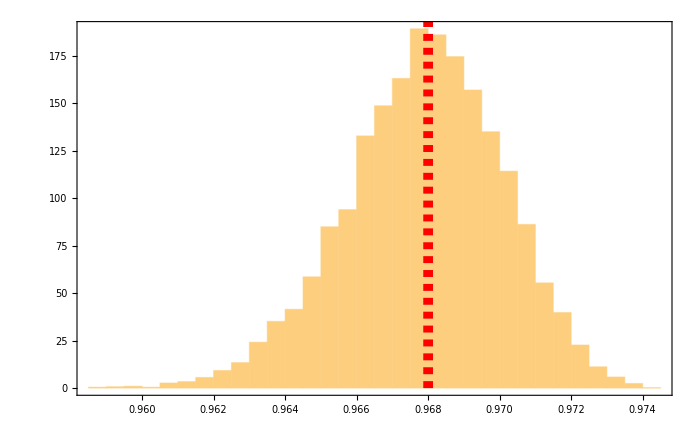

```mathematica
XiData=Table[SL@Xi[X],{j,1,2^13}];
Mean@XiData
StandardDeviation@XiData
Sqrt[Variance@XiData]
Histogram[XiData,Automatic,"PDF",
BaseStyle->{FontFamily->"Times New Roman",FontSize->22},
Frame->True,
FrameLabel->{Style[MaTeX["E(\Xi(M))",FontSize->22]],Style[MaTeX["\# \{M\}",FontSize->22]]},
RotateLabel->False,
TicksStyle->{{FontFamily->"Times New Roman",FontSize->20},{FontFamily->"Times New Roman",FontSize->20}},
Epilog->{{Thickness[.01], Dashed,{Red,Line[{{0.968,0},{0.968,250}}]}}},
ImageSize->700]
```

```mathematica
0.0021133873839685223^2
```

4.46641×10^-6

## SL-cube artwork

```mathematica
<<MaTeX`
```

```mathematica
Graphics3D[{
{Thick,Line[{{0,0,0},{1,1,1}},VertexColors->{Blue,Red}]},
{Thick,Red,Arrow@Line[{{0,0,0},{0,0,1}},VertexColors->{Blue,Red}]},
{Thick,Red,Arrow@Line[{{0,0,0},{0,1,0}},VertexColors->{Blue,Red}]},
{Thick,Red,Arrow@Line[{{0,0,0},{1,0,0}},VertexColors->{Blue,Red}]},
{Gray,Line[{{0,0,1},{0,1,1}}]},
{Gray,Line[{{0,0,1},{1,0,1}}]},
{Gray,Line[{{0,1,0},{0,1,1}}]},
{Dashed,{Gray,Line[{{0,1,0},{1,1,0}}]}},
{Dashed,{Gray,Line[{{1,0,0},{1,1,0}}]}},
{Gray,Line[{{1,0,0},{1,0,1}}]},
{Gray,Line[{{1,1,1},{0,1,1}}]},
{Gray,Line[{{1,1,1},{1,0,1}}]},
{Dashed,{Gray,Line[{{1,1,1},{1,1,0}}]}},
{Red,Sphere[{1,1,1},0.02]},
{Blue,Sphere[{0,0,0},0.02]},
{Black,Sphere[{1,1,0},0.02]},
Style[Text[Style[MaTeX["T_{36}, (1,1,1)",FontSize->22]],{1.04,1.02,1.05}],Black,16],
Style[Text[Style[MaTeX["J, (0,0,0)",FontSize->22]],{-0.04,-0.03,-0.04}],Black,16],
Style[Text[Style[MaTeX["S, (1,1,0)",FontSize->22]],{0.04,.63,0.41}],Black,16],
Style[Text[Style[MaTeX["E(M)",FontSize->22]],{-0.16,0.42,0.0}],Black,16],
Style[Text[Style[MaTeX["E(M^{\\rm R})",FontSize->22]],{-0.2,-0.38,0.3}],Black,16],
Style[Text[Style[MaTeX["E(M^{\\Gamma})",FontSize->22]],{-0.1,-0.18,0.67}],Black,16]
},
BoxStyle->Directive[White]]
```

-Graphics3D-

```mathematica
S=ArrayFlatten[Transpose[ArrayReshape[IdentityMatrix[36],{6,6,6,6}],{3,1,2,4}]];
```

```mathematica
SL/@{#,RF@#,T2@#}&[S]//N
```

{1.,1.,0.}